## Buffon' s Needle Sim

```mathematica
bn[d_,l_,n_]:=Module[{xs=Table[RandomReal[{0,d}],{i,1,n}],ts=Table[RandomReal[{0,Pi/2}],{i,1,n}]},
Table[If[xs[[i]]≤l Sin[ts[[i]]],1,0],{i,1,n}]
]
bnFrac[d_,l_,n_]:=Module[{os=bn[d,l,n]//DeleteCases[0]},
{(Length@os)/n//N,(2 l)/(Pi d)//N}
]
bnFrac[1,1,1000000]
```

{0.637646,0.63662}

## Random Telegraph Signal

## Attempt 1 : Switches per Interval

```mathematica
f=(#2^#1 E^-#2)/(#1!)&;
getN[rand_,λ_]:=Module[{distr=Table[PDF[PoissonDistribution[λ],k],{k,0,5 λ}],val=rand,n=0},
While[val>0,
val=val-distr[[1]];
distr=Drop[distr,1];
n=n+1
];
n
]
rts[λ_,intervals_]:=Module[{ns=Table[getN[RandomReal[],λ],{i,1,intervals}]},
Flatten[Table[Flatten[Table[{{(i/ns[[j+1]]+j),(-1)^i},{((i+1)/ns[[j+1]]+j),(-1)^i}},{i,0,ns[[j+1]]-1}],1],{j,0,Length@ns-1}],1]
]
processRTS[rts_,step_]:=Module[{d=rts[[Length@rts,1]]-5},
Table[Select[rts,#[[1]]>i&][[2,2]],{i,1,d,step}]
]
```

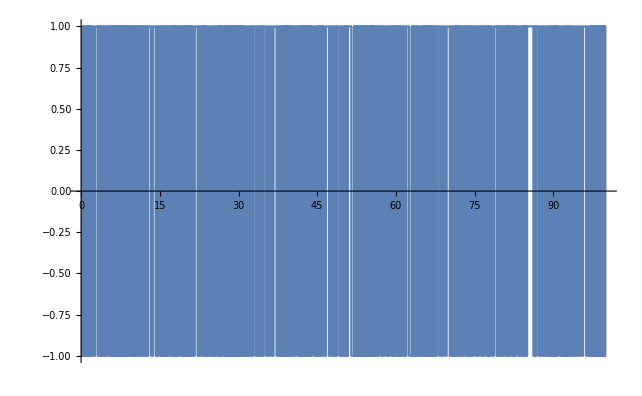

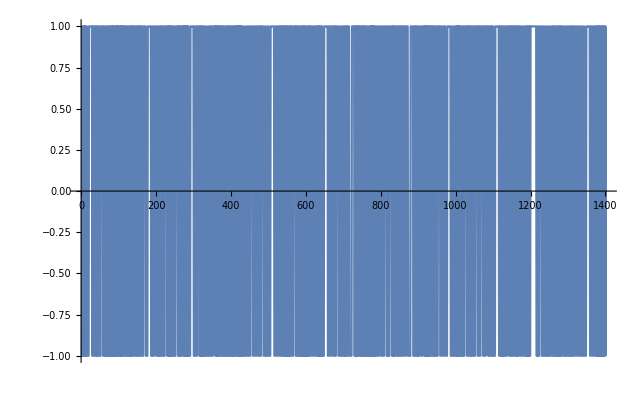

```mathematica
signal=rts[5,100];
ListPlot[signal,Joined->True]
processedSignal=processRTS[signal,0.07];
ListPlot[processedSignal,Joined->True]
```

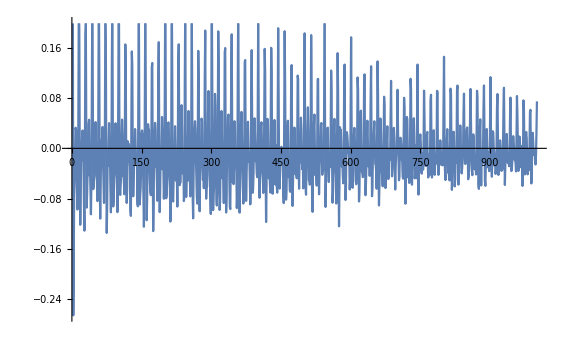

```mathematica
ListPlot[CorrelationFunction[processedSignal,{1000}],Joined->True]
```

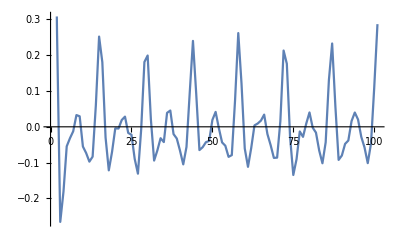

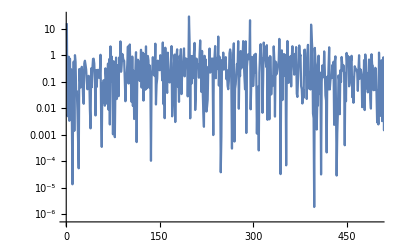

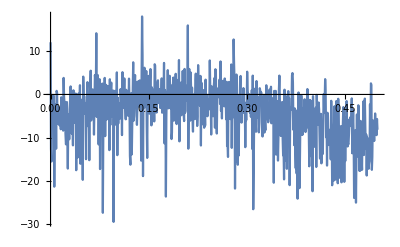

```mathematica
ListPlot[CorrelationFunction[processedSignal,{100}],Joined->True]
fft=Fourier[processedSignal];
ListLogPlot[Table[Re[fft[[i]]]^2,{i,1,Length@fft}],PlotRange->{{0,500},All},Joined->True]
Periodogram[processedSignal]
```

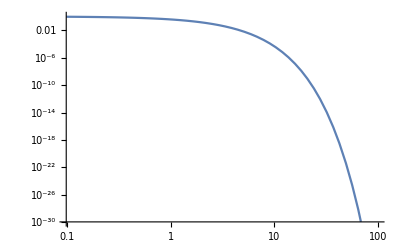

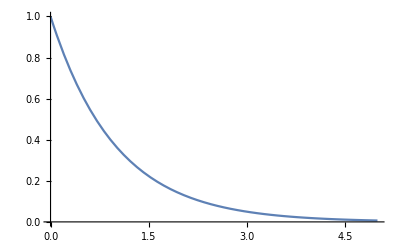

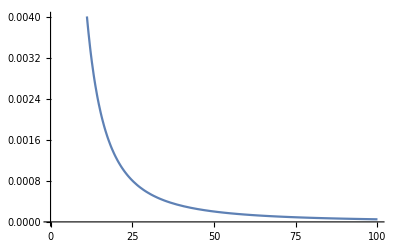

```mathematica
LogLogPlot[Exp[-t],{t,0,100}]
Plot[Exp[-t],{t,0,5}]
Plot[5/(Pi^2 f^2+5^2),{f,0,100}]
```

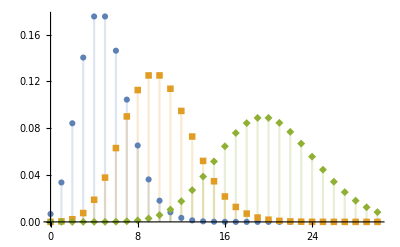

0.999975

```mathematica
DiscretePlot[Table[PDF[PoissonDistribution[λ],k],{λ,{5,10,20}}]//Evaluate,{k,0,30},PlotRange->All,PlotMarkers->Automatic]
Sum[PDF[PoissonDistribution[20],k],{k,0,40}]//N
```

```mathematica
"Today a "<>RandomWord["Adjective"]<>" "<>RandomWord["Noun"]<>" "<>RandomWord["Adverb"]<>" "<>RandomWord["Verb"]<>"ed"<>"."
```

Today a biologic manganese syntactically backstrokeed.

## Attempt 2 : Steps per Plateau

```mathematica
getN[rand_,λ_]:=Module[{distr=Table[PDF[PoissonDistribution[λ],k],{k,0,5 λ}],val=rand,n=0},
While[val>0,
val=val-distr[[1]];
distr=Drop[distr,1];
n=n+1
];
n
]
rts2[λ_,steps_]:=Module[{ns=Table[getN[RandomReal[],λ],{i,1,steps}]},
Flatten[Table[Table[(-1)^i,{j,1,ns[[i]]}],{i,1,Length@ns}],2]
]
```

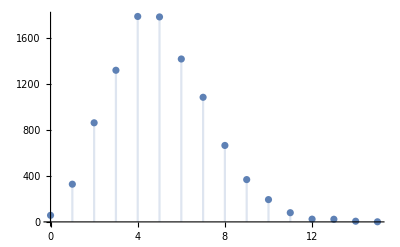

```mathematica
signal5=rts2[5,10000];
count=0;
pDistr=Table[If[signal5[[i]]≠signal5[[i+1]],count=0,count=count+1],{i,1,Length@signal5-1}];
zeros=Position[pDistr,0,1,Infinity];
DiscretePlot[Count[Table[pDistr[[zeros[[i,1]]-1]],{i,1,Length@zeros}],n],{n,0,15}]
```

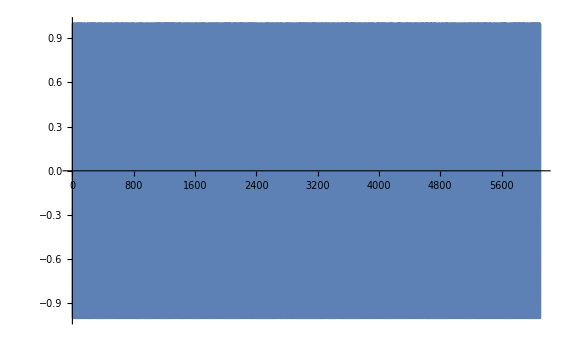

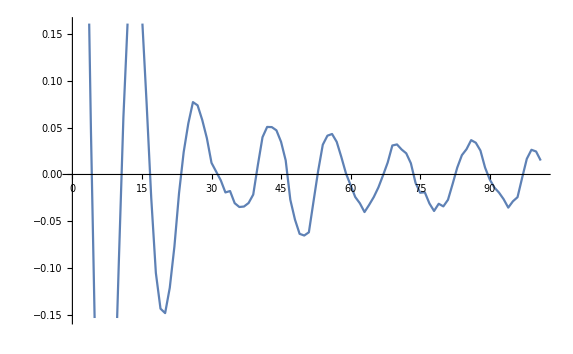

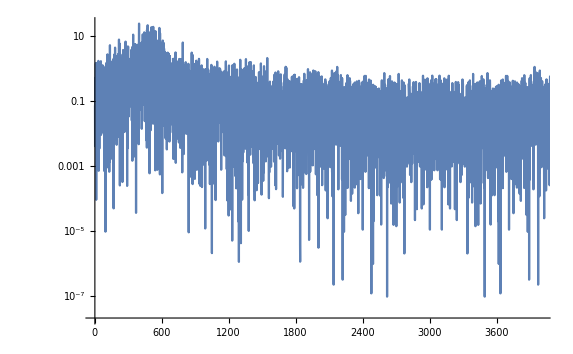

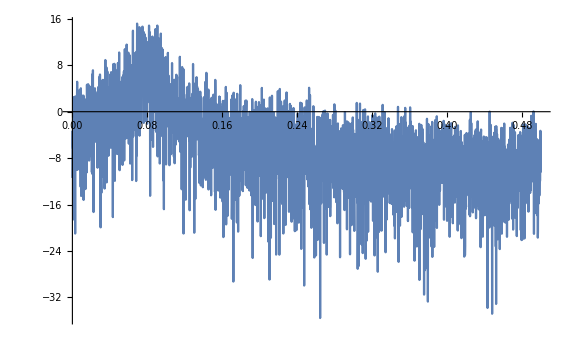

```mathematica
signal=rts2[5,1000];
ListPlot[signal,Joined->True]
ListPlot[CorrelationFunction[signal,{100}],Joined->True]
fft=Fourier[signal];
ListLogPlot[Table[Re[fft[[i]]]^2,{i,1,Length@fft}],PlotRange->{{0,4000},All},Joined->True]
Periodogram[signal]
```

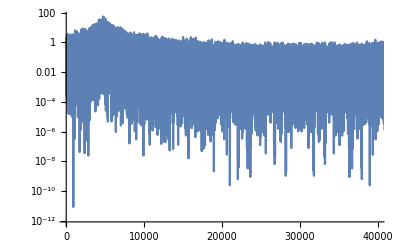

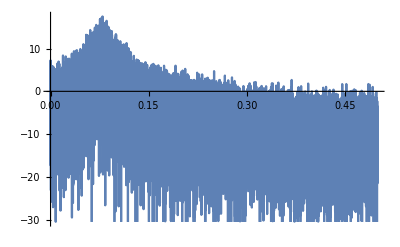

```mathematica
ListLogPlot[Table[Re[fft[[i]]]^2,{i,1,Length@fft}],PlotRange->{{0,40000},All},Joined->True]
Periodogram[signal]
```

## Using Built-In Functions

TemporalData[…]

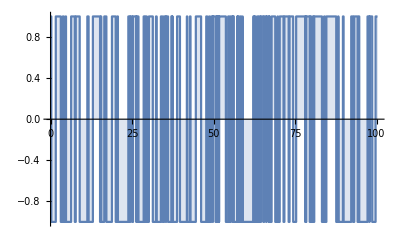

ⅇ^(-2 t λ)

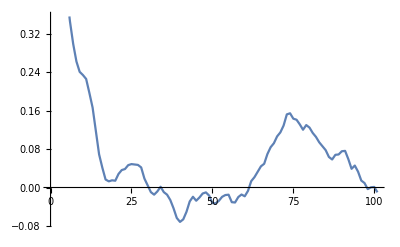

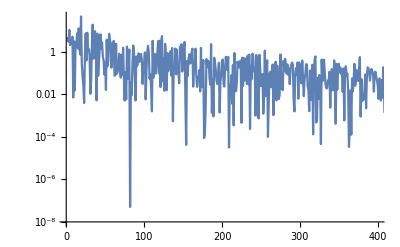

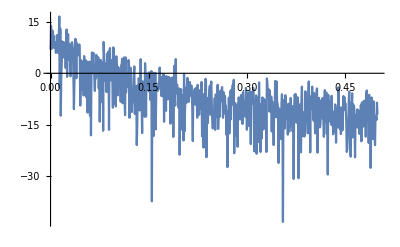

```mathematica
data=RandomFunction[TelegraphProcess[1.3],{0,100}]
ListStepPlot[data,Filling->Axis]
Mean[TelegraphProcess[λ][t]]
signal=processRTS[data["Path",All][[1]],0.07];
ListPlot[CorrelationFunction[signal,{100}],Joined->True]
fft=Fourier[signal];
ListLogPlot[Table[Re[fft[[i]]]^2,{i,1,Length@fft}],PlotRange->{{0,400},All},Joined->True]
Periodogram[signal]
```

Min[s,t]/(√(s t))

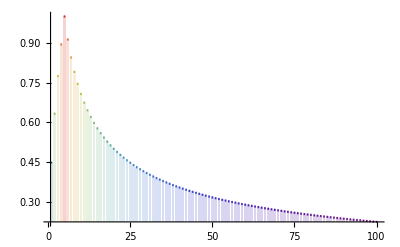

```mathematica
CorrelationFunction[BinomialProcess[p],s,t]
DiscretePlot[Evaluate[%/.{p->2/3,s->5}],{t,1,100},ExtentSize->1/2,ColorFunction->"Rainbow"]
```

```mathematica
Integrate[Exp[-Abs[2 λ t]-I w t],{t,-Infinity,Infinity}]
```

Piecewise[{{(4 Abs[λ])/(w^2+4 Abs[λ]^2), λ≠0&&2 Abs[λ]-Im[w]>0&&2 Abs[λ]+Im[w]>0}, {Integrate[ⅇ^(-ⅈ t w-2 Abs[t λ]),{t,-∞,∞},Assumptions→λ==0||2 Abs[λ]-Im[w]≤0||2 Abs[λ]+Im[w]≤0], True}}]

```mathematica
Assuming[λ>0&&RealQ[λ]&&RealQ[w]&&w>0,Integrate[Exp[-Abs[2 λ t]-I w t],{t,-Infinity,Infinity}]]
```

(4 λ)/((w-2 ⅈ λ) (w+2 ⅈ λ))